I’m computationally generating words that are the “average” of the same word in a bunch of different languages. I’m looking at the pronunciations and spelling of different words. Is there any way to generate an “average” word given the same word in two languages? Let’s start with the Spanish and French translation of “fish”.

```mathematica
rawTranslations = KeyValueMap[#1->First[#2]&,WordTranslation["fish", All]];
```

```mathematica
rawTranslations
```

{Mandarin Chinese→魚,Hindi→मछली,Spanish→pez,Russian→рыба,Indonesian→ikan,Portuguese→peixe,Bengali→মাছ,Arabic→سَمَكَة,Malay→ikan,Japanese→喉,French→poisson,German→Fisch,Urdu→مچهلی,Javanese→iwak,Turkish→balık,Telugu→చేప,Marathi→मासा,Vietnamese→cá,Korean→물고기,Tamil→மீன்,Thai→ปลา,Italian→pesce,Yue Chinese→鱼,Swahili→samaki,Northern Pashto→ټپ,Gujarati→માછલી,Polish→ryba,Ukrainian→риба,Hausa→kifi,Xiang Chinese→yu,Malayalam→മത്സം,Kannada→ಮೀನು,Burmese→ငါး,Oriya→ମାଛ,Hakka Chinese→魚,Panjabi→مچهی,Sundanese→lauk,Bhojpuri→मछरी,Maithili→माछ,South Azerbaijani→balıq,Romanian→peşte,Tagalog→isda,Dutch→vis,Sindhi→مڇي,Cebuano→isda,Igbo→azu,Amharic→ዓሣ,Nepali→माछा,Assamese→মাছ,Hungarian→hal,Madurese→juko',Khmer→រតី,Marwari→मछळी,Adamawa Fulfulde→liingu,Magahi→मछली,Somali→kalluun,Modern Greek→ψάρι,Serbian→riba,Czech→ryba,Shona→hove,Dari→ماهی,Qiubei Zhuang→bla,Zulu→inhlazi,Nyanja→nsomba,Lombard→pes,Belarusian→рыба,Bulgarian→риба,Swedish→fisk,Akan→nsuo mu nam,Kazakh→балық,Iloko→lames,Uighur→белиқ,Kinyarwanda→Jcinyanja,Xhosa→intlanzi,Hiligaynon→isda,Lingala→mbisi,Armenian→ձուկ,Catalan→peix,Tatar→балык,Minangkabau→lauk,Turkmen→balyk,Croatian→riba,Santali→हाकु,Afrikaans→vis,Danish→fisk,Kikuyu→thamaki,Finnish→kala,Hebrew→דג,Slovak→ryba,Eastern Balochi→ماهي، ماهيگ,Rundi→ifi,Norwegian→fisk,Kashmiri→गाड,Tibetan→ཉ་,Tswana→tlhapi,Basque→arrain,Georgian→თევზი,Pedi→hlapi,Wolof→jën,Central Bikol→sira,Buginese→bale,Tsonga→hlampfi,Galician→peixe,Eastern Yiddish→פיש,Kirghiz→балык,Lithuanian→žuvis,Achinese→eungkot,Kalenjin→njiriot,Zarma→hamisa,Esperanto→fiŝo,Slovenian→riba,Sidamo→qilxi'me,Bashkir→балыҡ,Chuvash→пулӑ,Swati→inhlanti,Makasar→juku,Macedonian→риба,Gusii→enswe,North Ndebele→ihlambi,Latvian→zivs,Tonga→ika,Tumbuka→somba,Teso→ekoleit,Newari→यां,Breton→pesk,Estonian→kala,Scots→iasg,Venda→khovhe,Chechen→чІара,Mapudungun→challwa,Ayacucho Quechua→challwa,Masai→sinkir,Erzya→кал,Krio→pwason,Fang→kuas,Kusaal→zīη,Kara-Kalpak→balıq,Sango→susu,Efik→iyak,Aklanon→isda,Maltese→ħuta,Yakut→балык,Samoan→i'a,Missing[NotAvailable]→pouissoun,Komi-Zyrian→чери,Fijian→ika,Icelandic→fiskur,Papiamento→piská,Moksha→кал,Kumyk→балыкъ,Navajo→łóó',Maori→ika,Gagauz→balık,Central Kaqchikel→kär,Dungan→йү,Kashubian→rëba,Kaba→kandje,Khakas→палых,Akaselem→ikuyu,Faroese→fiskur,Ga'anda→ekyenyanja,Romansch→pesch,Evenki→олло,Chorti→chay,Khanty→хуӆ,Chukot→ыннээн,Sanskrit→मीन,Chiripá→pira,Nanai→согдата,Choctaw→nani,Mansi→хул,Koryak→ынныын,Ho-Chunk→hóra,Karaim→балыкъ,Karon Dori→кол,Bai→sumuti,Batak→dekke,Gilyak→ч’о,Alabama→ɬaɬo,Judeo-Crimean Tatar→балых,Latin→piscis,Classical Quechua→challwa}

```mathematica
translatedList = Transliterate[Values[rawTranslations]]
```

{yu,machali,pez,ryba,ikan,peixe,macha,samakat,ikan,hou,poisson,Fisch,mchhly,iwak,balik,cepa,masa,ca,mulgogi,min,pla,pesce,yu,samaki,ټp,machali,ryba,riba,kifi,yu,matsam,minu,ငါး,macha,yu,mchhy,lauk,machari,macha,baliq,peste,isda,vis,mڇy,isda,azu,ዓሣ,macha,macha,hal,juko',រតី,machali,liingu,machali,kalluun,psari,riba,ryba,hove,mahy,bla,inhlazi,nsomba,pes,ryba,riba,fisk,nsuo mu nam,balykˌ,lames,belikˌ,Jcinyanja,intlanzi,isda,mbisi,juk,peix,balyk,lauk,balyk,riba,haku,vis,fisk,thamaki,kala,dg,ryba,mahy, mahyg,ifi,fisk,gada,ཉ་,tlhapi,arrain,tevzi,hlapi,jen,sira,bale,hlampfi,peixe,pys,balyk,zuvis,eungkot,njiriot,hamisa,fiso,riba,qilxi'me,balyҡ,pula,inhlanti,juku,riba,enswe,ihlambi,zivs,ika,somba,ekoleit,yam,pesk,kala,iasg,khovhe,cIara,challwa,challwa,sinkir,kal,pwason,kuas,zie,baliq,susu,iyak,isda,huta,balyk,i'a,pouissoun,ceri,ika,fiskur,piska,kal,balyk",loo',ika,balik,kar,jү,reba,kandje,palyh,ikuyu,fiskur,ekyenyanja,pesch,ollo,chay,huӆ,ynneen,mina,pira,sogdata,nani,hul,ynnyyn,hora,balyk",kol,sumuti,dekke,c'o,lalo,balyh,piscis,challwa}

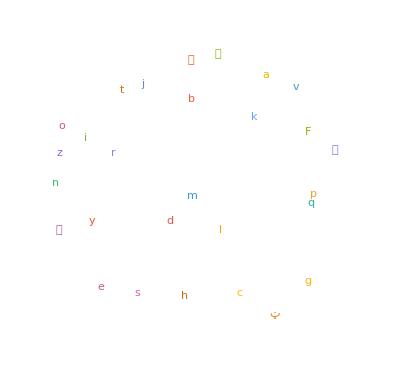

```mathematica
WordCloud[StringTake[translatedList, 1]]
```

```mathematica
audioSpanish=SpeechSynthesize[WordTranslation["fish", "Spanish"][[2]]]
```

```mathematica
audioFrench = SpeechSynthesize[WordTranslation["fish", "French"][[1]]]
```

```mathematica
audioEnglish=SpeechSynthesize[WordTranslation["fish", "English"][[1]]]
```

```mathematica
audioGerman = SpeechSynthesize[WordTranslation["fish", "German"][[1]]]
```

```mathematica
Spectrogram[audioSpanish]
```

-Graphics-

```mathematica
Spectrogram[audioFrench]
```

-Graphics-

```mathematica
ss=SpectrogramArray[audioSpanish]
```

```mathematica
sf=SpectrogramArray[audioFrench]
```

```mathematica
NetModel["Whisper-V1 Multilingual Turbo"]
```

NetGraph[<41>, <42>]

```mathematica
extractor=NetChain[{NetModel["Whisper-V1 Multilingual Turbo"],AggregationLayer[Max,1]}][AudioPartition[#,30][[1]]]&
```

NetChain[{NetModel[Whisper-V1 Multilingual Turbo],AggregationLayer[Max,1]}][AudioPartition[#1,30]⟦1⟧]&

```mathematica
audios={audioSpanish->"Spanish",audioFrench->"French",audioEnglish->"English", audioGerman->"German" };
```

```mathematica
FeatureSpacePlot[audios,FeatureExtractor->extractor,LabelingFunction->Callout]
```

-Graphics-

```mathematica
featuresEnglish = extractor[audioEnglish]
featuresGerman = extractor[audioGerman]
featuresFrench = extractor[audioFrench]
featuresSpanish = extractor[audioSpanish]
```

{0.78141,0.814744,0.762974,0.635075,0.845123,1.01385,0.741636,1.20936,1.26968,0.975297,0.843,1.02122,0.829691,0.781447,0.886289,1.18509,0.966145,0.970196,1.34603,1.17471,1.07549,1.17798,0.838697,0.910682,0.686461,0.748458,0.718972,0.796621,1.07864,0.809703,1.0226,0.752375,0.771165,0.823543,1.39047,0.97079,0.774704,0.96883,0.842773,0.945913,1.10041,1.01146,0.935374,0.980003,0.645776,1.21101,0.980109,0.955037,1.38107,0.983713,0.93314,0.763562,1.31294,0.818251,1.30186,1.19572,1.3617,1.16786,1.64009,1.08138,1.08383,3.0187,1.21562,1.19431,0.884377,1.05367,0.992677,1.33103,0.889289,1.39118,0.806587,1.09126,1.00457,0.815505,1.15346,0.930907,0.910454,1.01632,0.788771,0.859623,1.00933,0.877037,0.843913,0.956143,1.30522,1.00172,0.860057,0.799267,1.07221,1.06099,1.88987,0.758606,0.901616,0.478807,0.87584,1.10802,1.07112,0.75356,1.22594,0.960285,1.44158,0.956778,0.852355,0.764118,0.802091,0.863272,1.24274,0.830148,1.2604,0.936315,1.01617,1.32167,0.914099,1.12218,1.01074,0.946226,2.25362,1.15152,0.994884,0.993731,1.17332,0.855399,1.25098,1.2449,0.858647,0.957317,1.07814,0.848742,0.700472,0.834417,1.04017,1.06804,0.876558,0.996377,0.748079,0.928883,1.01504,0.962686,0.71025,1.1082,1.09744,1.28189,1.14564,1.1367,0.943368,0.91077,0.996364,0.995412,0.934207,0.924921,0.933702,3.95979,0.813121,0.894859,1.21774,0.918933,1.6978,0.892737,1.59645,1.12719,1.71925,1.11867,0.949015,0.831971,0.916585,0.954053,0.978829,0.820997,0.9475,0.721136,1.28024,1.47859,0.88811,0.986922,1.08348,1.14834,1.2232,1.18922,1.25294,0.862748,1.37895,0.784761,4.26179,0.73886,1.10559,1.20947,1.02366,0.662992,0.72759,1.0829,1.33107,0.995559,1.14848,1.15963,1.50453,1.28398,1.17897,1.43157,1.64185,1.2314,1.26619,1.10916,1.22863,0.998836,0.791027,0.811072,1.04409,0.975436,1.22022,0.806103,0.781133,0.799091,0.739956,0.89092,0.986504,1.3502,1.46732,0.99671,1.21735,1.0814,1.2685,0.848042,1.04206,1.33336,0.940822,0.703019,1.04546,2.7035,1.09098,1.32456,1.14681,2.61894,0.918635,0.693002,1.2351,1.19829,1.17242,0.96098,0.962229,0.968498,0.977544,1.13017,1.16861,0.831877,1.02567,0.896523,0.930204,1.27988,1.17623,0.857814,1.10221,0.797583,1.01641,0.875274,1.30527,0.844078,1.15349,1.30266,1.1992,0.950222,0.881483,0.866256,1.18711,0.952834,1.12924,1.21698,1.30377,0.788218,1.12259,0.897212,0.803959,1.18635,1.15129,1.16195,1.0381,0.89473,1.15416,1.05499,0.708317,0.600968,0.706977,1.03906,1.09234,1.07577,1.25009,0.851334,1.2988,0.971139,1.00452,1.18839,0.925439,0.888792,0.931742,0.947719,1.16109,1.09056,0.844994,0.800127,1.37487,1.37128,0.898833,0.851121,0.826397,1.30524,0.947316,0.635725,1.52259,1.06382,1.32735,1.14782,1.13099,0.781525,0.842204,1.19178,1.00953,0.855836,1.18754,1.24608,2.29586,7.19997,0.697219,0.905634,1.11839,1.14908,0.753319,0.836919,1.0521,0.83005,3.03825,0.641297,0.885762,1.2567,0.87353,0.956993,0.743994,0.820712,1.15713,1.22336,0.900487,0.954379,0.730392,1.06902,0.857125,1.1092,1.08422,0.846943,0.948936,0.950621,0.863268,1.1394,1.08133,1.37339,0.901451,1.1023,1.03993,1.10766,0.819456,1.15948,1.20159,1.07968,0.832436,1.16836,1.14497,1.173,1.25031,1.14067,0.879085,0.867704,1.30245,1.09821,1.16956,0.912622,1.03747,1.02146,1.19119,0.920761,1.04195,0.848674,1.35008,1.3076,1.08397,1.15717,0.930647,1.1792,0.812336,1.25613,0.958499,1.11754,1.03646,0.719723,0.922862,2.05395,2.3886,0.917178,1.31814,0.780194,0.956219,0.815039,1.2567,0.468825,0.73065,0.746183,0.658799,2.11426,0.940848,0.965804,1.09506,1.01554,0.80161,1.10641,1.00816,1.00934,1.11606,0.738005,0.967925,1.37742,1.02415,1.47577,1.05568,1.12557,0.96879,1.06843,0.671018,0.9154,0.91049,0.71801,1.09818,0.965613,0.715829,1.14345,1.06576,0.873127,1.08072,1.08894,1.24545,1.15105,0.879898,0.959865,1.07007,0.846423,1.38235,0.919074,0.898295,0.813891,1.24247,1.67904,0.950754,0.779099,1.2888,0.909573,1.14688,1.40724,0.934817,1.1446,0.82704,0.614044,0.797677,1.4965,0.963132,1.09047,0.985273,1.06566,1.06773,0.775859,0.774839,0.869241,1.80413,0.97424,1.00213,1.08191,1.12083,0.693514,1.29194,0.963476,1.19068,0.932635,1.14342,2.03415,0.87751,1.01233,0.870495,1.0109,1.15252,1.38293,0.938567,0.985694,1.05416,0.610318,1.01113,0.707747,0.872267,0.809061,0.862302,0.731692,0.890443,0.646666,1.30137,1.08444,1.25034,1.2497,0.942616,1.14319,0.86594,1.29249,0.957918,0.878057,0.861854,0.86843,0.9648,1.08746,0.804225,0.605949,0.747855,0.760959,0.825292,0.907956,0.838281,0.879727,1.11077,0.683928,0.89321,0.951916,1.20871,0.954093,0.719915,0.882093,0.864815,1.00585,0.801372,0.886772,0.925196,0.858052,1.15551,0.93881,1.15959,1.32395,0.80434,1.1997,0.911097,1.21499,0.944356,1.01329,0.760205,0.926689,1.64759,1.07355,0.739056,1.29807,0.938644,1.11829,0.924868,0.975858,1.59918,0.919982,1.09644,1.04662,0.60016,0.927956,1.27679,0.871386,0.855572,1.07662,0.927418,0.833776,0.778875,0.827451,0.764979,0.778869,0.720217,0.609705,0.781849,0.90692,0.812708,1.00181,1.15736,0.87146,1.13664,0.947884,0.931806,0.80767,1.11264,0.904609,0.895019,1.24776,0.858358,0.98935,1.66398,1.164,1.14067,1.2606,0.886365,0.813406,0.971115,0.935561,2.46361,1.12948,0.73905,0.754715,0.786614,0.781546,0.816604,0.862632,1.11005,0.85215,0.882908,0.855836,1.0043,1.07848,1.48894,0.733218,0.973533,1.29917,0.699538,0.66146,0.97047,1.23469,1.02899,1.38453,1.07555,1.12001,0.905015,0.784696,0.637055,1.32893,0.920199,1.2459,0.622721,0.937186,1.01093,1.03128,1.27544,0.830789,0.92425,1.06854,1.10162,10.0182,0.695425,0.93948,1.09516,1.08058,1.45705,0.827337,1.16066,1.04549,1.674,0.898532,0.958233,0.909788,1.03084,0.71584,0.840319,1.34593,0.822569,0.975695,1.04382,1.04763,1.24688,0.787364,0.796441,0.860475,0.881975,0.835351,1.12993,1.12645,0.930895,0.802429,0.865074,1.32162,0.693245,0.926744,1.02578,0.82765,0.842268,1.43824,0.806577,1.01997,1.12849,0.850646,0.913599,0.821576,1.15888,1.04437,0.966851,0.916742,1.21848,1.06333,1.09508,0.785585,1.23551,0.970339,1.13013,2.17152,0.917092,1.12516,1.14613,1.28087,1.22669,1.15627,0.941873,0.890165,0.8608,1.40175,1.22432,1.12684,0.890673,1.61974,0.775036,0.79959,0.670055,1.31198,0.958386,0.99432,0.719182,0.793399,0.987886,1.00738,1.22189,1.15542,1.10423,0.883677,0.994936,1.15913,0.921786,1.05191,1.28998,0.753756,0.900935,0.729079,1.19375,2.16517,1.17871,1.17663,1.20254,1.09836,0.906914,1.2458,1.0834,0.854989,1.20896,1.16394,1.00874,0.913663,1.01469,0.984751,1.09653,1.04652,0.727375,1.00446,0.993288,0.991172,1.25218,1.17199,1.60327,1.14615,1.00983,1.24116,2.40325,1.03979,1.04752,1.02619,1.02821,1.17456,0.949868,1.36904,1.13998,1.0051,0.707687,0.972328,1.08237,1.24539,0.911929,1.0495,0.849567,0.962616,0.980549,0.92417,0.895947,1.31099,1.19379,0.798954,1.28251,0.973615,0.834539,1.0755,1.20294,0.234026,0.779615,1.08648,0.891536,1.2552,0.772636,0.990486,1.04733,1.3631,1.31209,0.914952,1.02782,0.780462,1.33264,0.922002,1.88073,0.971821,0.935932,1.21993,1.07709,0.767317,0.864715,0.868732,1.06588,1.1643,1.0223,0.961037,0.698635,1.03521,0.927052,0.916519,1.1094,1.03438,1.04432,1.32411,1.12995,1.11773,1.21559,1.18099,1.19983,0.798349,1.59088,0.990248,0.992253,0.938182,1.27849,1.07953,1.13157,1.24527,1.07856,1.19793,0.878425,1.14771,1.38085,1.08525,0.964575,1.25516,1.23658,0.752815,1.07118,1.09196,1.2031,0.985245,0.832991,1.02897,0.861365,1.2214,0.983171,1.18101,1.13516,0.949801,0.902151,0.649852,0.888544,1.015,0.773427,1.22977,0.822734,0.778494,1.08429,1.12711,1.13357,1.08931,0.717602,0.978422,1.02353,0.903122,1.16858,0.870278,1.04754,0.787509,1.05031,1.21458,1.05931,1.45434,0.693878,0.903194,0.915072,0.918135,0.912185,1.01469,0.974709,0.756453,0.817639,1.37721,1.21945,1.01688,0.979185,0.975449,1.15119,1.03176,0.832417,0.919697,0.881053,0.944946,1.46621,0.895781,0.595096,1.06061,1.00471,1.06592,1.28483,1.17003,0.806927,0.736492,0.827461,1.15592,0.744572,1.23831,0.84906,1.57376,0.98117,1.2934,1.46519,1.02295,0.845569,0.957914,0.676102,0.788463,0.716131,1.26678,0.649701,1.33222,1.02151,1.05058,0.978827,1.05501,1.06357,1.18699,0.687826,1.34888,0.939218,0.851396,1.14193,0.9318,1.06884,1.38739,0.821273,1.41446,0.954833,0.836407,0.909917,0.866226,0.994054,1.33595,1.14263,1.30295,1.08058,1.03548,0.805675,0.906827,0.876318,0.63337,0.998064,0.739708,1.04736,0.825759,1.11705,0.662084,0.89463,0.888385,1.13345,1.17083,0.90433,1.07629,1.05253,0.879633,1.1568,1.41835,0.734413,0.944165,0.870466,1.36012,0.91581,1.28724,1.05537,1.19426,1.18023,0.98278,1.00099,0.915282,1.23116,6.62789,4.76214,0.892004,1.09321,0.829157,1.29456,0.946131,1.65783,0.600694,1.13492,1.02169,1.16188,1.11313,1.11976,1.34304,1.16372,1.15059,1.161,0.856625,1.20311,1.25897,1.37427,1.00907,0.866636,0.660295,0.838626,1.31862,0.960515,1.3256,0.876528,0.792141,1.10364,0.866329,0.835114,0.837246,1.07601,0.666127,1.23123,0.917109,0.853721,0.922003,1.08149,1.14494,1.95155,0.803164,0.778619,1.22017,1.01162,1.12176,0.930941,0.820654,0.872416,1.00071,0.660132,1.10113,0.965248,0.860612,1.09333,1.09959,0.987167,1.14026,1.2284,0.800785,1.15231,0.890463,1.14961,1.23107,0.844563,1.10141,0.886051,0.714012,1.21314,1.08199,0.659161,1.23015,0.654439,1.14521,0.920979,1.15882,0.897092,0.753672,0.953268,0.85366,0.992213,1.02491,1.034,0.744951,0.995607,3.03562,0.782372,0.888122,0.984744,0.831796,0.923845,0.89788,0.865142,0.814484,0.899831,1.01393,1.16246,1.11177,1.15493,0.99237,0.686742,0.929152,2.91096,1.15305,0.937755,1.04185,1.34609,1.22281,1.26136,1.25979,0.897663,1.08118,0.948605,0.7453,0.770668,0.922192,1.06921,1.02178,0.90821,1.2847,1.10703,0.954794,0.775508,0.916086,1.29421,0.997352,1.48835,0.971744,0.740211,0.857866,0.75684,0.794763,0.896429,0.81513,0.943186,1.04322,0.944747,1.04335,0.722067,0.690586,1.28723,0.866686,1.1604,1.00482,1.12844,0.911982,0.961292,1.12639,0.886106,1.41156,1.17804,0.850186,3.43188,0.907236,0.869482,0.893147,0.909176,1.32252,1.11953,2.41538,0.930893,0.81191,0.954574,1.08427,0.983575,0.700104,0.689931,0.995781,1.12337,1.00803,1.01786,0.95281,0.966506,1.25391,1.03318,0.869725,0.959256,1.13717,1.26074,0.989421,0.844855,1.09693,0.798729,0.846449,0.991289,0.920022,0.632647,1.09444,1.37912,1.15893,0.954915,0.733563,0.986002,0.80685,1.04961,0.808123,1.17367,1.1502,0.963985,0.788972,1.1023,0.680882,0.861567,1.58309,0.921836,1.0097,1.32384,1.27342,0.832051,0.990951,1.0727,0.790006,0.809453,1.08351,0.908564,0.673082,1.0167,0.998496,1.12837,1.02951,1.03737,0.939313,1.05757,0.843621,0.72341,1.4248,0.919287,0.686832,0.829202,1.18147,0.8514,1.01787,1.52149,1.01984,1.03164,1.11521,1.1391,1.04024,0.776661,0.925589,1.38769,0.85656,0.990985,0.80438,0.898333,1.17745,0.997493,0.788089,1.1068,0.984153,0.853631,0.848168,1.02514,0.76379,1.48048,1.11444,0.928949,1.02969,1.06415,0.990023,1.45002,0.830182,0.930551,0.912141,1.21561,0.811997,0.904367,0.805342,1.53746,0.933527,1.19395,0.760613,0.761749,1.15982,1.10267,1.01606,1.1974,0.746218,0.861726,0.87392,0.689136,0.961303,0.989327,0.975804,0.874242,0.763063,0.934608,0.873606,1.00748,0.77346}

{0.780581,0.779386,0.765226,0.631154,0.819793,0.891755,0.717985,1.17166,1.30795,0.951602,0.806036,1.09937,0.761495,0.765886,0.884777,1.26876,0.998973,0.955368,1.22288,1.18539,1.05514,1.17224,0.846354,0.903052,0.714729,0.719739,0.728643,0.79418,1.01294,0.908992,0.92026,0.751144,0.806163,0.796408,1.38862,1.04292,0.765332,0.827483,0.923923,0.893806,1.07849,1.067,0.918193,0.876605,0.826657,1.3868,0.9886,1.00036,1.35054,1.02747,0.867261,0.703847,1.29775,0.804996,1.39576,1.23182,1.35213,1.12606,1.40936,0.973522,1.04485,2.93613,1.14532,1.16143,1.01897,1.08912,1.06006,1.19025,0.817729,1.38287,0.80903,1.13304,0.892767,0.886708,1.13035,0.940749,1.01673,0.945577,0.824263,0.976928,0.967125,0.884183,0.818133,0.899374,1.2159,0.976905,1.01947,0.771883,1.01312,1.03637,1.89019,0.66371,0.951014,0.465976,0.92533,1.09937,0.911798,0.820561,1.14448,0.958229,1.26751,0.899372,0.841296,0.825694,0.739887,0.869331,1.17112,0.790492,1.26736,1.05743,0.949696,1.26345,0.919442,1.09776,1.045,0.867539,2.33282,1.18637,1.01466,0.862859,1.18861,0.814367,1.18707,1.25558,0.781507,0.925347,1.09031,0.832303,0.697059,0.752916,0.941067,0.962858,0.859647,0.962508,0.742314,1.03713,0.930208,1.04669,0.730013,1.03133,1.19722,1.25147,1.11991,1.09638,0.923148,0.79671,1.05435,1.00495,0.995554,0.899436,0.953728,4.02033,0.822016,0.884348,1.05398,0.95189,1.72519,0.894224,1.5235,1.12423,1.71467,1.10996,1.03693,0.829371,0.911695,0.924635,0.910571,0.835145,0.858027,0.841703,1.22649,1.4784,0.846615,0.982033,1.12115,1.17201,1.25296,1.22747,1.08495,0.896099,1.39436,0.818776,4.25208,0.720323,1.09462,1.2185,1.18095,0.579478,0.706975,1.16153,1.26306,0.966546,1.15126,1.15032,1.46418,1.37575,1.14606,1.42705,1.62507,1.21941,1.34326,1.07979,1.15466,1.06036,0.784494,0.848488,0.967829,0.942011,1.22302,0.792612,0.763507,0.773748,0.705357,0.865468,1.07127,1.21446,1.40186,0.936429,0.927518,1.0262,1.26807,0.84813,1.0676,1.42155,0.857725,0.684239,1.08504,2.72219,1.09767,1.34969,1.14061,2.56179,0.937676,0.96506,1.1854,1.23659,1.16315,1.08674,0.901794,1.08777,1.08143,1.13146,1.22777,0.989038,1.10129,0.950877,0.940224,1.2489,1.20829,1.01564,0.97159,0.914533,0.960022,0.84615,1.19694,0.834689,0.996536,1.32928,1.12995,0.940988,0.863437,0.764091,1.33964,1.00114,1.1392,1.1764,1.30748,0.852073,1.10654,0.922976,0.831982,1.11269,1.08747,1.14487,1.09485,0.859734,1.08823,1.00385,0.817771,0.578563,0.691548,1.06289,1.23916,1.09111,1.38986,0.837901,1.31749,0.945992,1.18878,1.20851,0.839826,0.849699,0.955199,0.816277,1.23726,0.91038,0.90735,0.820279,1.25292,1.35163,0.937114,0.918636,0.875287,1.29687,0.881337,0.578858,1.36372,0.983064,1.19254,1.16096,1.14078,0.752498,0.682537,1.21501,1.00128,0.903667,0.949678,1.15677,2.06002,7.1421,0.689861,0.876072,0.990347,1.16538,0.800459,0.993272,1.14434,0.959313,3.04494,0.59456,0.873869,1.1164,0.903358,0.954641,0.806518,0.801049,1.18842,1.2329,0.834946,0.918879,0.803582,1.07386,0.86534,1.01394,1.09075,0.81556,0.926429,0.827498,0.86009,1.09787,1.01345,1.36265,0.962907,1.07364,1.01673,1.1023,0.809354,1.05059,1.22456,1.16035,0.789987,1.11801,1.15122,1.09905,1.25996,1.10431,0.759156,0.860453,1.31856,1.33348,1.05598,0.902944,1.02649,1.02735,1.15903,0.955101,1.08519,0.812913,1.38858,1.31918,0.979043,1.18416,1.01464,1.16466,0.826072,1.1376,0.881801,1.11912,1.08083,0.640449,0.847845,2.05409,2.38167,0.974129,1.2859,0.69487,0.811217,0.871494,1.23036,0.467632,0.742159,0.75934,0.660037,2.10003,0.933219,1.12066,1.05669,1.05283,0.815836,1.05416,0.997303,0.987212,1.11864,0.740522,0.976245,1.36555,1.07194,1.4106,1.06241,1.07961,0.998711,1.05271,0.651886,0.94282,0.951776,0.787887,1.00879,0.955623,0.851948,1.16321,0.966963,0.985093,1.01191,1.05587,1.27154,1.05477,0.918758,0.943245,1.08927,0.836886,1.41375,0.919727,0.769523,0.818451,1.16785,1.64481,0.978583,0.776875,1.29938,0.894388,1.14288,1.41052,0.928299,1.07047,0.810721,0.603158,0.959933,1.38823,0.904418,0.93868,1.01872,1.11262,1.02366,0.802124,0.716187,0.946401,1.77773,1.05496,1.02456,1.10432,1.05864,0.700808,1.05774,0.972279,1.21898,0.918942,1.10051,2.08294,0.880125,1.0965,0.915119,0.999721,1.25271,1.37013,0.971147,0.93991,1.02724,0.637706,0.923135,0.719551,0.84767,0.875377,0.712724,0.766306,0.945545,0.616612,1.29338,1.03386,1.2618,1.22179,1.03616,1.1204,0.939961,1.29829,0.97503,0.91065,0.841631,0.86377,1.04354,1.01002,0.741655,0.596078,0.729401,0.758951,0.804365,0.902991,0.845375,0.905089,1.0696,0.680412,0.934099,1.0058,1.13912,0.888835,0.710321,0.867062,0.839996,1.05779,0.875216,0.849945,0.876153,0.988205,1.12133,0.919626,1.17203,1.10492,0.849436,1.25125,1.15293,1.27884,0.955302,1.09107,0.859682,0.873174,1.61856,1.07176,0.911891,1.51564,0.897907,1.13057,1.19136,0.92435,1.69245,0.880352,0.953748,1.05111,0.722308,0.833244,1.0982,0.876415,0.940932,1.00112,0.941164,0.869393,0.802264,1.16968,0.74046,0.718841,0.705439,0.628487,0.739542,0.918674,0.791865,0.940341,1.12183,0.931889,1.09686,0.96452,0.91378,0.771293,1.10112,0.887946,0.903085,1.22177,0.906132,1.13309,1.60564,1.00739,1.14127,1.27376,0.728608,0.827305,0.995181,0.817413,2.46583,1.11705,0.725506,0.772594,0.722679,0.80346,0.824109,0.874539,1.11635,0.899771,0.899088,0.809154,0.990567,1.05683,1.48329,0.79097,0.991882,1.33239,0.670909,0.749218,1.05177,1.29415,0.968524,1.30043,1.06858,1.14361,0.912723,0.882803,0.554846,1.31695,0.795213,1.20559,0.64459,0.985743,1.07944,1.0174,1.36324,0.950854,0.861244,0.961446,1.09138,10.1322,0.828893,0.929697,1.01843,1.15308,1.39855,0.953908,1.12666,0.966472,1.55202,0.892028,0.907714,0.920196,1.00001,0.692983,0.825904,1.32965,0.847378,0.938936,0.991827,1.061,1.3903,0.848918,0.673366,0.892879,0.931182,0.868815,1.02687,1.11118,0.90587,0.783223,0.849201,1.27765,0.68486,0.978023,1.04865,0.80632,0.847321,1.40667,0.77015,0.97409,1.04405,0.792103,0.945785,0.798652,1.11473,0.950283,1.0683,0.888832,1.43563,1.08432,1.0941,0.778493,1.27103,0.976851,1.07358,2.15204,0.916111,1.10649,1.17041,1.24102,1.1707,1.14705,0.950639,0.787547,0.870651,1.44141,1.27359,1.2999,0.751372,1.68375,0.757679,0.767156,0.667862,1.09802,0.83267,0.986055,0.780765,0.702959,1.056,1.02759,1.21294,1.01158,1.10375,1.24916,0.995524,1.08861,0.920623,1.05043,1.25723,0.812764,0.72528,0.692867,1.20739,2.05282,1.17612,1.18864,1.19205,1.0993,0.920402,1.24101,1.10913,0.949558,1.01493,1.16147,0.91717,0.907191,1.02331,0.985399,1.07838,1.02428,0.690954,1.08723,0.91074,1.00426,1.37393,1.1271,1.57701,1.16833,0.918876,1.29305,2.25426,1.04755,1.06543,1.07597,1.06566,1.11829,0.911413,1.32982,1.14166,1.0551,0.704796,0.984335,1.0772,1.18962,0.924061,1.02845,0.762054,0.96533,1.00127,0.913754,0.859388,1.35845,1.059,0.832537,1.27305,0.943252,0.919,1.03052,1.21343,0.209833,0.733837,1.03188,0.869481,1.28322,0.799605,0.924277,1.01941,1.38618,1.27595,0.917734,1.16031,0.770774,1.2146,0.887038,1.85949,0.918169,0.926392,1.15958,1.16018,0.756256,0.823506,1.08189,1.03842,1.12892,0.998736,1.04106,0.71328,0.994919,0.933424,1.04321,1.08249,1.05747,1.12301,1.34093,1.19404,1.11083,1.25556,1.18874,1.21455,0.748406,1.63699,1.08285,1.00869,0.937941,1.30604,1.04626,1.18099,1.19769,1.03668,1.16829,0.947202,1.1933,1.35146,1.05712,0.987802,1.25611,1.31104,0.688,1.06736,1.02419,1.19518,0.968423,0.868999,0.972224,0.868671,1.14317,1.03556,1.17694,1.34022,0.951288,0.942391,0.689292,0.878673,0.971746,0.841488,1.23345,0.78602,0.881979,1.01283,0.97165,1.11491,1.07776,0.767264,0.94121,1.08858,0.898535,1.12003,0.843697,1.06873,0.882022,1.02065,1.20362,1.0167,1.36416,0.714045,0.838252,0.864944,0.876412,1.04056,1.06354,0.862912,0.738461,0.837588,1.48985,1.20973,1.07554,0.932409,1.0213,1.25682,0.87532,0.925815,0.890623,0.86788,0.794327,1.45554,0.882121,0.613402,1.12622,0.973725,1.01884,1.10279,1.22377,0.850697,0.738536,0.813364,1.17373,0.685259,1.22023,0.842269,1.69282,1.01655,1.10965,1.40204,0.98579,0.894815,0.959844,0.684476,0.755204,0.842303,1.32271,0.645938,1.41716,0.989796,1.06814,0.942069,1.05398,1.04774,1.23862,0.682042,1.09707,0.926921,0.878307,1.05922,1.0839,1.08813,1.47181,0.810695,1.36971,1.00668,0.89603,0.885281,0.918927,0.984179,1.21498,1.22857,1.2728,0.95374,1.0912,0.771523,0.886695,0.88873,0.610851,1.00909,0.706397,1.05945,0.940324,1.12769,0.687257,0.965103,0.815799,1.19509,1.1664,0.890446,0.963585,1.15999,0.905018,1.32979,1.26347,0.608348,0.959286,1.01906,1.37834,0.868026,1.18209,1.02692,1.29591,1.27416,0.981084,1.04788,0.932312,1.261,6.68824,4.73698,0.907022,1.10209,0.817025,1.07025,0.925967,1.62992,0.602834,1.10859,1.01432,1.19233,1.21014,1.01499,1.28963,1.15735,1.19528,1.1658,1.11774,1.16453,1.24315,1.36816,1.04697,0.821957,0.644523,0.763732,1.31305,0.873191,1.29516,0.999342,0.863561,1.03201,0.83043,0.974198,0.858222,1.08808,0.833026,1.13364,0.830826,0.843028,0.897424,1.08964,1.22606,1.93329,0.855611,0.716414,1.2644,0.951739,1.08787,0.90287,0.617069,0.797756,0.934235,0.681551,1.08285,0.987248,1.00863,1.09363,1.17689,0.940252,1.05158,1.32156,0.77957,1.1151,0.936423,1.0547,1.20765,0.862105,1.06109,0.898398,0.654326,1.16552,1.08294,0.643279,1.13908,0.631966,1.13221,1.01415,1.08199,0.898119,0.808132,0.934566,0.777177,0.901488,0.924033,0.981507,0.776431,0.97684,2.97569,0.776882,1.02343,0.787068,0.825149,1.0081,1.00633,0.885199,0.814156,0.910426,1.05952,1.06289,0.987053,1.13132,1.00903,0.687599,0.897718,2.91587,1.11556,0.932049,1.05052,1.24527,1.25053,1.22448,1.22756,0.938251,1.08567,0.930346,0.736171,0.764568,1.00786,1.03525,1.01348,0.891173,1.18536,0.960147,0.930271,0.819906,1.02683,1.03524,1.00524,1.47504,0.961843,0.720059,0.918574,0.814365,0.769068,0.874027,0.709135,1.04445,0.968886,0.943584,1.17953,0.810027,0.723745,1.1338,0.899879,1.25361,0.928924,1.05386,0.863883,0.960132,1.16239,0.909732,1.38131,1.16356,0.795117,3.42986,0.974016,0.867762,0.887312,0.944545,1.36082,1.11106,2.41174,0.889896,0.808918,0.943108,0.983233,0.863335,0.703291,0.721998,0.926247,1.18727,0.993467,1.04191,0.940629,0.950685,1.26744,1.13517,0.976131,1.01306,1.07163,1.24292,0.883342,0.867024,1.14833,0.77503,0.893255,0.916661,0.943331,0.620881,1.1624,1.37153,1.12886,0.854324,0.914425,0.975143,0.796739,1.16541,0.827787,1.07301,1.1297,1.15736,0.791321,1.0576,0.739747,0.7709,1.55656,1.00734,0.976479,1.32019,1.2987,0.900474,1.02502,1.10909,0.895631,0.929648,1.09298,0.893678,0.677386,1.03904,0.986717,1.11396,0.946831,1.01533,0.859898,1.02959,0.830344,0.727132,1.32572,0.828038,0.775097,0.810418,1.10904,0.857925,0.946778,1.5766,1.03778,1.09687,1.12711,0.95825,1.01815,0.836255,0.928189,1.38748,0.955949,1.02609,0.766424,0.862689,1.24408,1.04345,0.889106,1.06702,1.1021,0.85774,0.90253,0.840318,0.707096,1.48221,1.18409,0.933334,1.02671,1.08131,1.07357,1.29577,0.800254,0.932042,0.93407,1.13255,0.784912,0.812791,0.781309,1.53533,0.934381,1.21295,0.704802,0.777701,1.15537,1.10475,0.997318,1.17977,0.775898,1.03415,0.845058,0.696088,0.920335,0.989276,0.936056,0.952488,0.731187,0.971606,0.887446,0.984423,0.783104}

```mathematica
Length[featuresEnglish]
Length[featuresFrench]
Length[featuresGerman]
Length[featuresSpanish]
```

1280

1280

1280

«1 more identical outputs»